```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_MPI/plotting_routines

## Reference Solution (N=40)

```mathematica
Clear[θRef]
```

```mathematica
θRef[x_] = 0.9884735156696915 x-1.1457678311582425*^-10 (Cosh[1.2078840101317283 x]-Sinh[1.2078840101317283 x])+1.1457678311728836*^-10 (Cosh[1.2078840101317283 x]+Sinh[1.2078840101317283 x])+6.933239237405841*^-10 (Cosh[1.3078453876891523 x]-Sinh[1.3078453876891523 x])-6.933239237401193*^-10 (Cosh[1.3078453876891523 x]+Sinh[1.3078453876891523 x])-2.1060693855761778*^-8 (Cosh[1.4201039622641722 x]-Sinh[1.4201039622641722 x])+2.1060693855765543*^-8 (Cosh[1.4201039622641722 x]+Sinh[1.4201039622641722 x])-2.6992029959027656*^-7 (Cosh[1.5481284098563823 x]-Sinh[1.5481284098563823 x])+2.699202995902824*^-7 (Cosh[1.5481284098563823 x]+Sinh[1.5481284098563823 x])-4.210084451095493*^-6 (Cosh[1.6964567741916035 x]-Sinh[1.6964567741916035 x])+4.210084451095377*^-6 (Cosh[1.6964567741916035 x]+Sinh[1.6964567741916035 x])-0.00003118740478035235 (Cosh[1.8716019970135933 x]-Sinh[1.8716019970135933 x])+0.000031187404780352396 (Cosh[1.8716019970135933 x]+Sinh[1.8716019970135933 x])-0.00014648630693050077 (Cosh[2.084723525254245 x]-Sinh[2.084723525254245 x])+0.00014648630693049947 (Cosh[2.084723525254245 x]+Sinh[2.084723525254245 x])-0.00039749988958803415 (Cosh[2.3577417474531877 x]-Sinh[2.3577417474531877 x])+0.0003974998895880341 (Cosh[2.3577417474531877 x]+Sinh[2.3577417474531877 x])-0.0007222957924572226 (Cosh[2.7318724706353126 x]-Sinh[2.7318724706353126 x])+0.0007222957924572248 (Cosh[2.7318724706353126 x]+Sinh[2.7318724706353126 x])-0.0009273335235258298 (Cosh[3.282073516752524 x]-Sinh[3.282073516752524 x])+0.0009273335235258277 (Cosh[3.282073516752524 x]+Sinh[3.282073516752524 x])-0.0009098029667887219 (Cosh[4.162412100887137 x]-Sinh[4.162412100887137 x])+0.0009098029667887222 (Cosh[4.162412100887137 x]+Sinh[4.162412100887137 x])-0.0005701566488494193 (Cosh[5.7687839178768066 x]-Sinh[5.7687839178768066 x])+0.0005701566488494196 (Cosh[5.7687839178768066 x]+Sinh[5.7687839178768066 x])-0.0001268351754459892 (Cosh[9.551054823962051 x]-Sinh[9.551054823962051 x])+0.0001268351754459892 (Cosh[9.551054823962051 x]+Sinh[9.551054823962051 x])-1.3502774955260917*^-8 (Cosh[28.55918996701305 x]-Sinh[28.55918996701305 x])+1.3502774955260907*^-8 (Cosh[28.55918996701305 x]+Sinh[28.55918996701305 x]);
```

## Analytical

```mathematica
Do[resultAna[ii]=GetSolution[ii,0.1,1,bcMBC[ii]]⟦3⟧;
errorAna[ii]=Abs[NIntegrate[(x)(resultAna[ii]-θRef[x]),{x,-0.5,0.5}]];,{ii,4,20,2}];
```

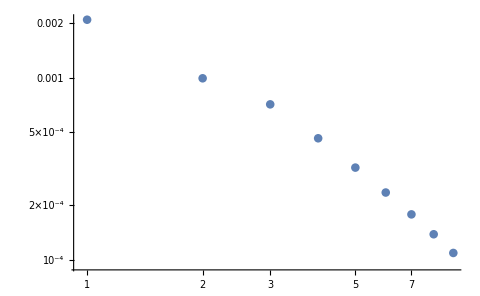

```mathematica
ListLogLogPlot[Table[errorAna[ii],{ii,4,20,2}]]
```

```mathematica
Plot[]
```

0.0226504